```mathematica
$HistoryLength = Infinity;

c2subs=(-u[1])/(Conjugate@u[4])Conjugate[u[3]-c[3]];
addend1=Conjugate@u[4](c[2](u[2]-c[2])-u[1]c[3]);
addend2=u[1](c[2]Conjugate@c[3]+u[1]Conjugate[u[2]-c[2]]);
simplify=Replace[Simplify@#,Conjugate[x_]:>SuperStar@x,Infinity]&;
simplifyConj=Replace[#,Conjugate[x_]:>SuperStar@x,Infinity]&;
xyReal=Replace[#,{Conjugate[x]->x,Conjugate[y]->y},Infinity]&;

normalizePhase[l_]:=Exp[-I Arg@First@l]l
```

### The equation whose solution (here denoted c[3]) gives a reachable state, which also gives the target state after projection, is addend1-addend2==0, with c[2] replaced as per c2subs:

```mathematica
addend1-addend2/.c[2]->c2subs//FullSimplify
```

-1/Abs[u[4]]^2 u[1] (Abs[u[4]]^2 (Conjugate[u[2]] u[1]+(-Conjugate[c[3]]+Conjugate[u[3]]) u[2])+Abs[u[1]]^2 Conjugate[u[4]] (-c[3]+u[3])+(c[3] Conjugate[u[4]]^2+(2 Conjugate[c[3]]^2-3 Conjugate[c[3]] Conjugate[u[3]]+Conjugate[u[3]]^2) u[1]) u[4])

### equationToSolve is the final expression to solve, in terms of x and y which are respectively real and imaginary part of c[3]

```mathematica
equationToSolve=FullSimplify[
addend1-addend2/.c[2]->c2subs
]/.c[3]->x+I y//xyReal//Collect[#,{x,y},FullSimplify]&;
equationToSolve
```

-(2 x^2 u[1]^2)/Conjugate[u[4]]+(2 y^2 u[1]^2)/Conjugate[u[4]]+x ((4 ⅈ y u[1]^2)/Conjugate[u[4]]+u[1] (-Conjugate[u[4]]+(3 Conjugate[u[3]] u[1])/Conjugate[u[4]]+u[2]+Abs[u[1]]^2/u[4]))+u[1] (-Conjugate[u[2]] u[1]-(Conjugate[u[3]]^2 u[1])/Conjugate[u[4]]-Conjugate[u[3]] u[2]-(Abs[u[1]]^2 u[3])/u[4])-1/Abs[u[4]]^2 ⅈ y u[1] (-Abs[u[1]]^2 Conjugate[u[4]]+Abs[u[4]]^2 u[2]+(Conjugate[u[4]]^2+3 Conjugate[u[3]] u[1]) u[4])

The above is a quadratic form with complex coefficients, as shown here:

```mathematica
equationToSolve//xyReal//CoefficientList[#,{x,y}]&//simplifyConj//Grid[#,Frame->All]&
```

u[1] (-u[2]^* u[1]-((u[3]^*)^2 u[1])/u[4]^*-u[3]^* u[2]-(Abs[u[1]]^2 u[3])/u[4]) | -((ⅈ u[1] (-Abs[u[1]]^2 u[4]^*+Abs[u[4]]^2 u[2]+((u[4]^*)^2+3 u[3]^* u[1]) u[4]))/Abs[u[4]]^2) | (2 u[1]^2)/u[4]^*
u[1] (-u[4]^*+(3 u[3]^* u[1])/u[4]^*+u[2]+Abs[u[1]]^2/u[4]) | (4 ⅈ u[1]^2)/u[4]^* | 0
-(2 u[1]^2)/u[4]^* | 0 | 0

### We now create random (normalized) target amplitudes, to test whether the solutions of equationToSolve actually work:

```mathematica
randomAmps=Normalize@RandomComplex[{-1-I,1+I},4];
ampsReplRules=MapIndexed[u[First@#2]->#1&,randomAmps]
```

{u[1]→-0.0214402+0.469058 ⅈ,u[2]→-0.496035+0.327117 ⅈ,u[3]→-0.179726-0.0413925 ⅈ,u[4]→-0.502643-0.373904 ⅈ}

The actual equation, with the randomly chosen target amplitudes given above, looks like the following:

```mathematica
equationToSolve/.ampsReplRules//Expand
```

(-0.160375-0.150693 ⅈ)-(0.241128+0.226986 ⅈ) x-(0.524074+0.469876 ⅈ) x^2-(0.440647-0.385393 ⅈ) y-(0.939753-1.04815 ⅈ) x y+(0.524074+0.469876 ⅈ) y^2

Numerically, there seem to be two real solutions to the above equation:

```mathematica
ContourPlot[
Abs[equationToSolve/.ampsReplRules],
{x,-.6,-.2},{y,-.8,.8},
PlotRange->All,ColorFunction->"Rainbow",Contours->100,PlotPoints->50
]
```

-Graphics-

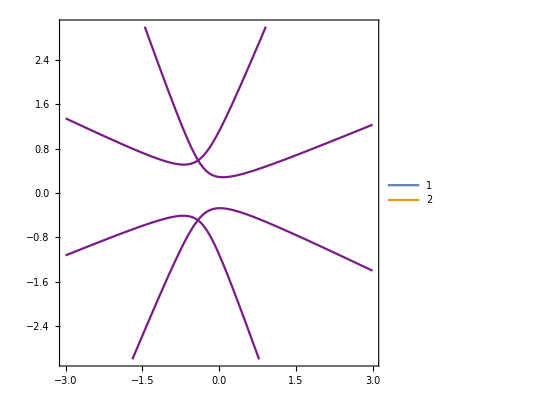

```mathematica
ContourPlot[
Evaluate@{realEquation==0,
imagEquation==0},
{x,-3,3},{y,-3,3},
PlotRange->All,ColorFunction->"Rainbow",Contours->100,PlotPoints->50,PlotLegends->Automatic
]
```

### To numerically solve the equation we split it into two equations, containing respectively real and imaginary parts of the coefficient. The resulting system of 2 real quadratic forms is then easily solved with NSolve

```mathematica
equationToSolve/.ampsReplRules//Expand
realEquation=Replace[
equationToSolve/.ampsReplRules//Expand,
Complex[r_,i_]:>r,
Infinity
]
imagEquation=Replace[
equationToSolve/.ampsReplRules//Expand,
Complex[r_,i_]:>i,
Infinity
]
```

(-0.160375-0.150693 ⅈ)-(0.241128+0.226986 ⅈ) x-(0.524074+0.469876 ⅈ) x^2-(0.440647-0.385393 ⅈ) y-(0.939753-1.04815 ⅈ) x y+(0.524074+0.469876 ⅈ) y^2

-0.160375-0.241128 x-0.524074 x^2-0.440647 y-0.939753 x y+0.524074 y^2

-0.150693-0.226986 x-0.469876 x^2+0.385393 y+1.04815 x y+0.469876 y^2

```mathematica
First@Solve[D[realEquation,x]==0,x]
First@Solve[D[realEquation,y]==0,y]
```

{x→-0.954064 (0.241128+0.939753 y)}

{y→0.954064 (0.440647+0.939753 x)}

```mathematica
Solve[
D[realEquation,x]==0&&
D[realEquation,y]==0,
{x,y}
]
```

{{x→-0.336489,y→0.118715}}

```mathematica
solutionsForC3=NSolve[
{realEquation==0,
imagEquation==0},
{x,y},
Reals
]
```

{{x→-0.410574,y→0.589336},{x→-0.4154,y→-0.490319}}

Let us take the first of the found real solutions:

```mathematica
c3=solutionsForC3⟦1,All,2⟧//Apply@Complex
c3⋄2=solutionsForC3⟦2,All,2⟧//Apply@Complex
```

-0.410574+0.589336 ⅈ

-0.4154-0.490319 ⅈ

```mathematica
c2=(-randomAmps⟦1⟧)/(Conjugate@randomAmps⟦4⟧)Conjugate[randomAmps⟦3⟧-c3]
c2⋄2=(-randomAmps⟦1⟧)/(Conjugate@randomAmps⟦4⟧)Conjugate[randomAmps⟦3⟧-c3⋄2]
```

-0.475531-0.165216 ⅈ

0.148733+0.349715 ⅈ

### Now that the coefficients c_2 and c_3 have been found, we carry on building the corresponding final state, and using it to compute all the coin parameters leading to it:

```mathematica
outAmps={
{randomAmps⟦1⟧,0},
{randomAmps⟦2⟧-c2,c2},
{randomAmps⟦3⟧-c3,c3},
{0,randomAmps⟦4⟧}
};
outAmps⋄2={
{randomAmps⟦1⟧,0},
{randomAmps⟦2⟧-c2⋄2,c2⋄2},
{randomAmps⟦3⟧-c3⋄2,c3⋄2},
{0,randomAmps⟦4⟧}
};
{outAmps//MF,outAmps⋄2//MF}
```

{(-0.0214402+0.469058 ⅈ | 0
-0.0205039+0.492334 ⅈ | -0.475531-0.165216 ⅈ
0.230848-0.630728 ⅈ | -0.410574+0.589336 ⅈ
0 | -0.502643-0.373904 ⅈ),(-0.0214402+0.469058 ⅈ | 0
-0.644767-0.0225972 ⅈ | 0.148733+0.349715 ⅈ
0.235674+0.448926 ⅈ | -0.4154-0.490319 ⅈ
0 | -0.502643-0.373904 ⅈ)}

Verify that the reachability condition is met for this state:

```mathematica
outAmps⟦1,1⟧/outAmps⟦2,2⟧+Conjugate[outAmps⟦4,2⟧/outAmps⟦3,1⟧]//Chop
```

0

```mathematica
isOutputFromQW[outAmps,4]
```

True

Verify that the resulting state does indeed produce the correct target after projection of the coin over + (the normalization is still disregarded here):

```mathematica
randomAmps
Total/@outAmps
Total/@(outAmps⋄2)
```

{-0.0214402+0.469058 ⅈ,-0.496035+0.327117 ⅈ,-0.179726-0.0413925 ⅈ,-0.502643-0.373904 ⅈ}

{-0.0214402+0.469058 ⅈ,-0.496035+0.327117 ⅈ,-0.179726-0.0413925 ⅈ,-0.502643-0.373904 ⅈ}

{-0.0214402+0.469058 ⅈ,-0.496035+0.327117 ⅈ,-0.179726-0.0413925 ⅈ,-0.502643-0.373904 ⅈ}

```mathematica
{randomAmps==Total/@outAmps,
randomAmps==Total/@(outAmps⋄2)}
```

{True,True}

We can now use the obtained final state to trace back the whole quantum walk evolution:

```mathematica
computedParameters={};
FoldList[
backwardStep[#1,
AppendTo[computedParameters,parsFromAmps[#1,#2]];
Last@computedParameters
]&,
outAmps,{4,3,2}
]//Map@MF
```

{(-0.0214402+0.469058 ⅈ | 0
-0.0205039+0.492334 ⅈ | -0.475531-0.165216 ⅈ
0.230848-0.630728 ⅈ | -0.410574+0.589336 ⅈ
0 | -0.502643-0.373904 ⅈ),(-0.650274-0.225929 ⅈ | 0
-0.618174+0.32195 ⅈ | -0.480065+0.206027 ⅈ
0 | 0.315678-0.862503 ⅈ
0 | 0),(-0.794137+0.340817 ⅈ | 0
0 | -1.0226+0.532579 ⅈ
0 | 0
0 | 0),(0 | -1.3241+0.568259 ⅈ
0 | 0
0 | 0
0 | 0)}

```mathematica
computedParameters⋄2={};
FoldList[
backwardStep[#1,
AppendTo[computedParameters⋄2,parsFromAmps[#1,#2]];
Last[computedParameters⋄2]
]&,
outAmps⋄2,{4,3,2}
]//Map@MF
```

{(-0.0214402+0.469058 ⅈ | 0
-0.644767-0.0225972 ⅈ | 0.148733+0.349715 ⅈ
0.235674+0.448926 ⅈ | -0.4154-0.490319 ⅈ
0 | -0.502643-0.373904 ⅈ),(0.236415+0.555882 ⅈ | 0
-0.720709-0.107296 ⅈ | -0.279599+0.469143 ⅈ
0 | 0.374611+0.713581 ⅈ
0 | 0),(-0.416909+0.699538 ⅈ | 0
0 | -1.07465-0.159989 ⅈ
0 | 0
0 | 0),(0 | -0.695132+1.16637 ⅈ
0 | 0
0 | 0
0 | 0)}

```mathematica
computedParameters
computedParameters⋄2
```

{{0.820192,4.42368},{0.649152,0.739782},{0.643196,3.21635}}

{{0.680417,0.4478},{0.73508,5.34361},{0.643196,1.96046}}

The incorrect normalization of the obtained states is not an issue here. It arises simply because we neglected the normalization factors when projecting at the end. Renormalizing and choosing a conventional phase is enough to recover the correct result.

Here we use the above parameters to reconstruct the whole dynamics, from an initial state with the coin in the R state:

```mathematica
fullReconstructedDynamics=FoldList[
Dot[
shiftCoinGeneralOp[4,#2],
#1
]&,
SparseArray[{2->1},8],
Table[Append[thetaAndXi,0],{thetaAndXi,Reverse@computedParameters}]
];
reconstructedFinalState=Partition[#,2]&@Last@fullReconstructedDynamics;
reconstructedFinalStateNormalized=reconstructedFinalState//Flatten//normalizePhase//Partition[#,2]&;
fullReconstructedDynamics//Map[MF@Partition[#,2]&]
reconstructedFinalStateNormalized//MF
```

{(0 | 1
0 | 0
0 | 0
0 | 0),(0.599756 | 0
0 | 0.797948-0.059767 ⅈ
0 | 0
0 | 0),(0.352883+0.322073 ⅈ | 0
0.482369-0.0361298 ⅈ | 0.362559
0 | -0.4374+0.46367 ⅈ
0 | 0),(0.142058-0.293279 ⅈ | 0
0.147831-0.30838 ⅈ | 0.258055+0.235525 ⅈ
-0.319861+0.339071 ⅈ | 0.423154-0.26348 ⅈ
0 | 0.218228+0.376039 ⅈ)}

(0.325873 | 0
0.341981-0.00138677 ⅈ | -0.0994737+0.334917 ⅈ
-0.444594-0.140057 ⅈ | 0.421592+0.265971 ⅈ
0 | -0.243296+0.360327 ⅈ)

```mathematica
fullReconstructedDynamics⋄2=FoldList[
Dot[
shiftCoinGeneralOp[4,#2],
#1
]&,
SparseArray[{2->1},8],
Table[Append[thetaAndXi,0],{thetaAndXi,Reverse[computedParameters⋄2]}]
];
reconstructedFinalState⋄2=Partition[#,2]&@Last[fullReconstructedDynamics⋄2];
reconstructedFinalStateNormalized⋄2=reconstructedFinalState⋄2//Flatten//normalizePhase//Partition[#,2]&;
fullReconstructedDynamics⋄2//Map[MF@Partition[#,2]&]
reconstructedFinalStateNormalized⋄2//MF
```

{(0 | 1
0 | 0
0 | 0
0 | 0),(0.599756 | 0
0 | 0.303974+0.740198 ⅈ
0 | 0
0 | 0),(0.262539-0.35916 ⅈ | 0
0.203859+0.496411 ⅈ | 0.402224
0 | 0.310201-0.506049 ⅈ
0 | 0),(0.304833-0.163292 ⅈ | 0
0.22881+0.416431 ⅈ | 0.165168-0.225954 ⅈ
0.195153-0.318364 ⅈ | -0.153575+0.447675 ⅈ
0 | -0.047031+0.458975 ⅈ)}

(0.345814 | 0
0.00505771+0.475125 ⅈ | 0.252289-0.121185 ⅈ
0.322356-0.188486 ⅈ | -0.346765+0.322105 ⅈ
0 | -0.258183+0.382376 ⅈ)

In all the steps the states are correctly normalized, as expected:

```mathematica
Norm@*Flatten/@fullReconstructedDynamics
Norm@*Flatten/@(fullReconstructedDynamics⋄2)
```

{1,1.,1.,1.}

{1,1.,1.,1.}

```mathematica
reconstructedFinalState//MF
```

(0.142058-0.293279 ⅈ | 0
0.147831-0.30838 ⅈ | 0.258055+0.235525 ⅈ
-0.319861+0.339071 ⅈ | 0.423154-0.26348 ⅈ
0 | 0.218228+0.376039 ⅈ)

And... the result after the projection is exactly what it should be:

```mathematica
{Total/@reconstructedFinalStateNormalized//Normalize//MF,
Total/@(reconstructedFinalStateNormalized⋄2)//Normalize//MF}
```

{(0.469547
0.349426+0.480581 ⅈ
-0.0331428+0.181429 ⅈ
-0.350563+0.519192 ⅈ),(0.469547
0.349426+0.480581 ⅈ
-0.0331428+0.181429 ⅈ
-0.350563+0.519192 ⅈ)}

```mathematica
randomAmps//normalizePhase//MF
```

(0.469547
0.349426+0.480581 ⅈ
-0.0331428+0.181429 ⅈ
-0.350563+0.519192 ⅈ)